```mathematica
f[k_] := 1/k;
suma =Sum[(-1)^(k-1)*f[k], {k, 1, Infinity}] (*1*)
```

Log[2]

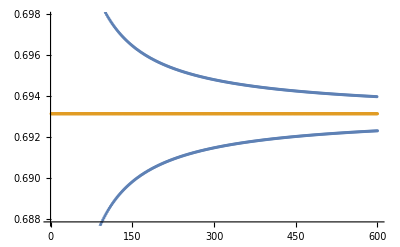

```mathematica
n = 600; (*2*)
ListPlot[{Table[Sum[(-1)^(k-1)*f[k], {k, 1, x}], {x, 1, n}], Table[Log[2], {x, 1, n}]}]
```

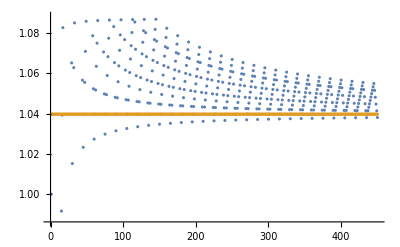

```mathematica
(*3*)
p = 10;
q = 5;
rep = 30;
ser = Table[(-1)^(k-1)*f[k], {k, 1, n}];
pos = Partition[Select[ser, (# > 0)&,  rep*p], p] ;
neg = Partition[Select[ser, (# < 0)&,  rep*q], q] ;
s =Flatten[ Table[{pos[[k]],neg[[k]]}, {k, 1, rep}]];
K =  Limit[k*f[k],k->Infinity];
Ocekavani = suma + 1/2 * K * Log[p/q];

ListPlot[{Accumulate[s], Table[Ocekavani, {x, 1, rep*(p+q)}]}]
```

```mathematica
(*4*)
prerovnani[g_[k_], cislo_] := (
suma = Sum[(-1)^(k-1)*g[k], {k, 1, Infinity}] ;
K = Limit[k*g[k],k->Infinity];
pomer = N[Exp[2*(cislo - suma)/K ]];
pomer = Rationalize[pomer,10^(-2)];
p = Numerator[pomer];
q = Denominator[pomer];

rep = 30;
ser = Table[(-1)^(k-1)*f[k], {k, 1, rep * (p+q + 1)}];
pos = Partition[Select[ser, (# > 0)&,  rep*p], p] ;
neg = Partition[Select[ser, (# < 0)&,  rep*q], q] ;
s =Flatten[ Table[{pos[[k]],neg[[k]]}, {k, 1, rep}]];

ListPlot[{Accumulate[s], Table[cislo, {x, 1, rep*(p+q)}]}]
)

prerovnani[f&, 1.3]
```

Table::iterb: Iterator {f,1,30 (2+ⅇ^((2 (13/10-Sum[«2»]))/Limit[Times[«2»],Rule[«2»]]))} does not have appropriate bounds.

Select::innf: Non-negative integer or Infinity expected at position 3 in Select[Table[(-1)^(f-1) f[f],{f,1,30 (2+ⅇ^(2 Power[«2»] Plus[«2»]))}],#1>0&,30 ⅇ^((2 (13/10-Sum[Times[«2»],{«3»}]))/(lim_(f→DirectedInfinity[«1»]) f («1»&)))].

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[Select[Table[(-1)^(f-1) f[f],{f,1,30 (2+ⅇ^Times[«3»])}],#1>0&,30 ⅇ^((2 (13/10-Sum[«2»]))/Limit[Times[«2»],Rule[«2»]])],ⅇ^((2 (13/10-∑_(f=1)^DirectedInfinity[«1»] Power[«2»] («1»&)))/(lim_(f→∞) f (f&)))].

Table::argm: Table called with 0 arguments; 1 or more arguments are expected.

Limit::ivar: 1 is not a valid variable.

Table::iterb: Iterator {f,1,30 (2+ⅇ^((2 (13/10-Sum[«2»]))/Limit[«1»&,Rule[«2»]]))} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Limit::ivar: 1 is not a valid variable.

General::stop: Further output of Limit::ivar will be suppressed during this calculation.

Select::innf: Non-negative integer or Infinity expected at position 3 in Select[Table[(-1)^(f-1) f[f],{f,1,30 (2+ⅇ^(2 Power[«2»] Plus[«2»]))}],#1>0&,30 ⅇ^((2 (13/10-Sum[Times[«2»],{«3»}]))/(lim_(1→DirectedInfinity[«1»]) (f&)))].

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[Select[Table[(-1)^(f-1) f[f],{f,1,30 (2+ⅇ^Times[«3»])}],#1>0&,30 ⅇ^((2 (13/10-Sum[«2»]))/Limit[«1»&,Rule[«2»]])],ⅇ^((2 (13/10-∑_(f=1)^DirectedInfinity[«1»] Power[«2»] («1»&)))/(lim_(1→∞) (f&)))].

Select::innf: Non-negative integer or Infinity expected at position 3 in Select[Table[(-1)^(f-1) f[f],{f,1,30 (2+ⅇ^(2 Power[«2»] Plus[«2»]))}],#1>0&,30 ⅇ^((2 (13/10-Sum[Times[«2»],{«3»}]))/(lim_(1→DirectedInfinity[«1»]) (f&)))].

General::stop: Further output of Select::innf will be suppressed during this calculation.

Part::partw: Part 1 of Table[] does not exist.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[Select[Table[(-1)^(f-1) f[f],{f,1,30 (2+ⅇ^Times[«3»])}],#1>0&,30 ⅇ^((2 (13/10-Sum[«2»]))/Limit[Times[«2»],Rule[«2»]])],ⅇ^((2 (13/10-∑_(f=1)^DirectedInfinity[«1»] Power[«2»] («1»&)))/(lim_(2→∞) 2 (f&)))].

General::stop: Further output of Partition::ilsmp will be suppressed during this calculation.

Part::partw: Part 2 of Table[] does not exist.

Part::partw: Part 3 of Partition[Select[Table[(-1)^(f-1) f[f],{f,1,30 (2+ⅇ^Times[«3»])}],#1>0&,30 ⅇ^((2 (13/10-Sum[«2»]))/Limit[Times[«2»],Rule[«2»]])],ⅇ^((2 (13/10-∑_(f=1)^DirectedInfinity[«1»] Power[«2»] («1»&)))/(lim_(3→∞) 3 (f&)))] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NSum::nsnum: Summand (or its derivative) (-1)^(-1+f) (f&) is not numerical at point f = 46662.

General::stop: Further output of NSum::nsnum will be suppressed during this calculation.